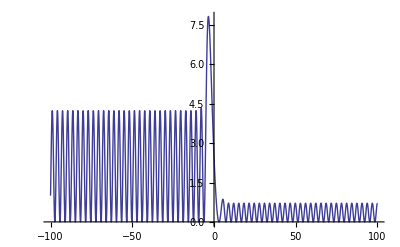

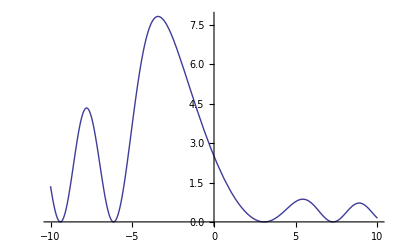

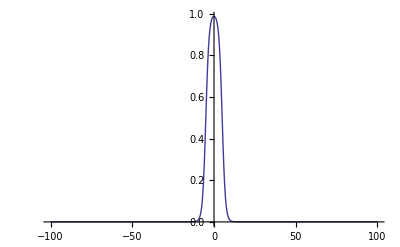

```mathematica
ClearAll["Global`*"]
ℏ =1;
m=1;
λ =1.0;
s=0.5;
k =5;
v=0.5;
d= 100;
V[t]=v*(Tanh[s(t+k)]-Tanh[s(t-k)]);
sols = Map[First[NDSolve[{-x''[t] + (V[t]- λ)x[t] == 0, x[-d] ==1, x'[d] == 0},x,t, Method->{"Shooting", "StartingInitialConditions"->{x[-d] ==0, x'[-d] == #}},MaxStepSize->0.001,MaxSteps->500000]]&,
{1}];
Plot[Abs[Evaluate[x[t] /. sols]]^2, {t,-d,d},PlotRange->All]
Plot[Abs[Evaluate[x[t] /. sols]]^2, {t,-10^-1 d,d*10^-1},PlotRange->All]
Plot[Evaluate[V[t]],{t,-d,d},PlotRange->All,PlotPoints->29,MaxRecursion->5]
```

```mathematica
*
```